```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA"}]]
```

Successfully patched FeynArts.

```mathematica
FCClearScalarProducts[];
SP[p,p]=s;
```

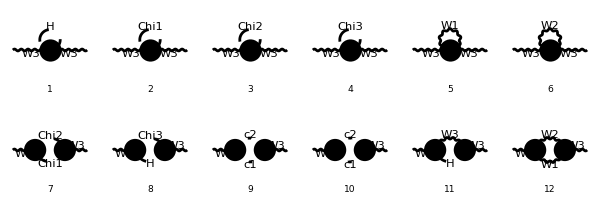

```mathematica
LoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],V[3] -> V[3], InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA", "Photonless_Weak_gaugeonly_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA", "Photonless_Weak_gaugeonly_FA"}]];
Paint[LoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{6,2},ImageSize->{600,200}];
AmpLoop[0]=Contract/@FCFAConvert[CreateFeynAmp[LoopDiags,Truncated->True,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]/(2π)^4;
```

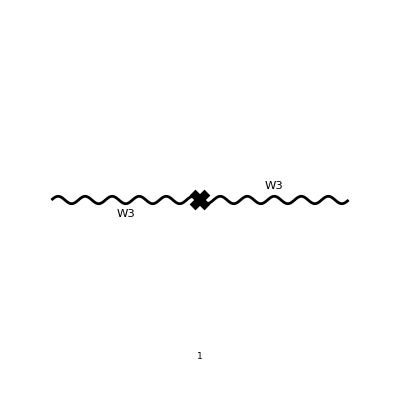

```mathematica
CTDiags = InsertFields[CreateCTTopologies[1, 1 -> 1,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],V[3] -> V[3], InsertionLevel->{Particles}, Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA", "Photonless_Weak_gaugeonly_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA", "Photonless_Weak_gaugeonly_FA"}]];
Paint[CTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{1,1},ImageSize->{100,100}];
AmpCT[0]=Contract/@FCFAConvert[CreateFeynAmp[CTDiags,Truncated->True,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},ChangeDimension->4,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]/(2π)^4;
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
AmpLoop[1]=AmpLoop[0]//processLoop//FCReplaceAll[#,vH->2 mW/gW]&;
AmpTotal[0]=(AmpLoop[1]+Total[AmpCT[0]])/ⅈ//Expand;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
AmpTotal[1]=AmpTotal[0]//Collect2[#,Pair[Momentum[p],LorentzIndex[Lor1]],Head->Const0]&//Collect2[#,MetricTensor[LorentzIndex[Lor1],LorentzIndex[Lor2]],Head->Const1]&;
```

```mathematica
RNCond1=Simplify[AmpTotal[1]/.{s->mW^2},Assumptions->mW>0]//Re//ComplexExpand//Refine[#,Assumptions->{mW>2mh>0}]&;
RNCond2=Simplify[D[AmpTotal[1],s]/.{s->mW^2},Assumptions->mW>0]//Re//ComplexExpand//Refine[#,Assumptions->{mW>2mh>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mW},{}),FR$deltaZ({W3,W3},{{}})}];
```

```mathematica
AmpTotal[2]=(AmpTotal[1]/.RNRes[[1]])/.ScaleMu->1//Expand//FullSimplify;
```

```mathematica
AmpTotal[3]=AmpTotal[2]/.{mW->1,mh->0.3,gW->0.6};
```

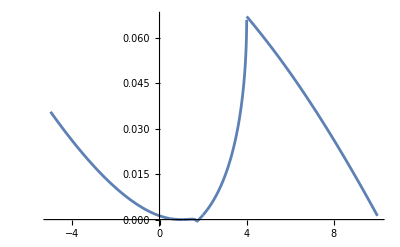

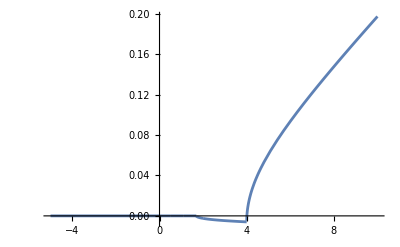

```mathematica
Plot[Re[AmpTotal[3]],{s,-5,10},PlotRange->Full,MaxRecursion->10]
Plot[Im[AmpTotal[3]],{s,-5,10},PlotRange->Full,MaxRecursion->10]
```

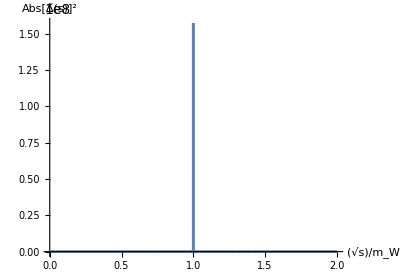

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+AmpTotal[3]]^-2},{s,0,4},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, W],Abs[OverTilde[Δ][s]]^2}],AspectRatio->0.7]
```

```mathematica
Series[AmpTotal[2],{s,0,4},Assumptions->{mW>2mh>0,0<s<mh^2}]/.mW->1//Simplify
```

-(gW^2 (mh^2-1)^3 (2 log(mh)-log(mh^2)))/(384 π^2 s^2)+(gW^2 (mh^2-9) (mh^2-1) (2 log(mh)-log(mh^2)))/(384 π^2 s)+1/(384 π^2 (mh^4-5 mh^2+4))gW^2 (-(mh^2-4) (2 (3 mh^8-18 mh^6+50 mh^4-56 mh^2+3) log(mh)-(mh^2-1) (6 mh^4-21 mh^2-(mh^2-9) log(mh^2)+84 √3 π-391))-6 mh √(4-mh^2) (mh^8-8 mh^6+27 mh^4-48 mh^2+28) arg(mh^2+ⅈ √(-mh^2 (mh^2-4))))+1/(1152 π^2)gW^2 s (-(6 (2 mh^6-13 mh^4+32 mh^2-36) mh^2 arg(mh^2+ⅈ √(-mh^2 (mh^2-4))))/(√(-mh^2 (mh^2-4)))+(-12 mh^8+60 mh^6+(39-54 √3 π) mh^4+4 (√((mh^2-1)^2)+27 √3 π-57) mh^2+2 √((mh^2-1)^2)+3 (mh^2-1)^2 log(mh^2)-54 √3 π+81)/((mh^2-1)^2)+(6 (2 mh^14-17 mh^12+66 mh^10-145 mh^8+188 mh^6-2 (√((mh^2-1)^2)-24) mh^2-(2 √((mh^2-1)^2)+129) mh^4-13) log(mh))/((mh^2-1)^4))+1/(768 π^2 (mh^2-1)^6)gW^2 s^2 ((mh^2-1) (30 mh^10-148 mh^8+(11 √((mh^2-1)^2)+202) mh^2-√((mh^2-1)^2)+(3 √((mh^2-1)^2)+316) mh^6+19 (√((mh^2-1)^2)-20) mh^4-20)-8 mh^2 (mh^6+(3 √((mh^2-1)^2)-5) mh^2+√((mh^2-1)^2)+(√((mh^2-1)^2)-7) mh^4+11) log(mh))+1/(26880 π^2 (mh^2-1)^8)gW^2 s^3 ((mh^2-1) (111 mh^14-777 mh^12+2296 mh^10+28 (24 √((mh^2-1)^2)+139) mh^2-28 √((mh^2-1)^2)-28 (√((mh^2-1)^2)+100) mh^8+7 (156 √((mh^2-1)^2)+235) mh^6+7 (316 √((mh^2-1)^2)-633) mh^4+64)-280 mh^2 (mh^8+2 (3 √((mh^2-1)^2)+8) mh^2+√((mh^2-1)^2)+(√((mh^2-1)^2)-4) mh^6+6 (√((mh^2-1)^2)-4) mh^4+11) log(mh))+1/(11520 π^2 (mh^2-1)^10)gW^2 s^4 ((mh^2-1) (7 mh^18-63 mh^16+252 mh^14-539 mh^12+(390 √((mh^2-1)^2)+1739) mh^2-10 √((mh^2-1)^2)+10 (5 √((mh^2-1)^2)+109) mh^10+(270 √((mh^2-1)^2)-977) mh^8+4 (475 √((mh^2-1)^2)-738) mh^6+(1960 √((mh^2-1)^2)+1403) mh^4+40)-120 mh^2 (mh^10+2 (5 √((mh^2-1)^2)+24) mh^2+√((mh^2-1)^2)+√((mh^2-1)^2) mh^8+5 (2 √((mh^2-1)^2)-9) mh^6+5 (4 √((mh^2-1)^2)-3) mh^4+11) log(mh))+O(s^(9/2))